Real-World Data

A central feature of the Wolfram Language is that it’s got immense amounts of real-world data built in. It’s got data on countries and animals and movies, and lots more. It gets all this from the Wolfram Knowledgebase, which is being updated all the time—and is what powers Wolfram|Alpha and services based on it.

But how can you talk about a country in the Wolfram Language? The easiest way is just to use plain English. You can tell the Wolfram Language you’re going to be giving it plain English by pressing ctrl= (hold down the Control key and press the = key), or on a touch device, by pressing the  button.

```mathematica
LinguisticAssistant
```

Enter the plain English “united states”:

```mathematica
LinguisticAssistant
```

As soon as you press return (or click away), the Wolfram Language will try to interpret what you typed. Assuming it succeeds, it’ll display a little yellow box that represents a Wolfram Language entity. In this case, it’s the entity corresponding to the United States.

```mathematica
LinguisticAssistant
```

Press the check mark to confirm that’s what you want:

```mathematica
Entity["Country","UnitedStates"]
```

Now you can ask for lots of properties of this entity. Like you could ask for the US flag.

Ask for the flag property of the United States:



```mathematica
Entity["Country","UnitedStates"]["Flag"]
```

The result you get is something you can go on doing computation with—like in this case image processing.

Color-negate the US flag:

```mathematica
ColorNegate[-Graphics-]
```

-Graphics-

If all you want to do is to get the US flag, you can just ask for it in English.

```mathematica
LinguisticAssistant
```

-Graphics-

EntityValue is a more flexible way to ask for the values of properties.

Use EntityValue to get the US flag:

```mathematica
EntityValue[Entity["Country","UnitedStates"],"Flag"]
```

-Graphics-

EntityValue also works with lists of entities.

Get flags for a list of countries:

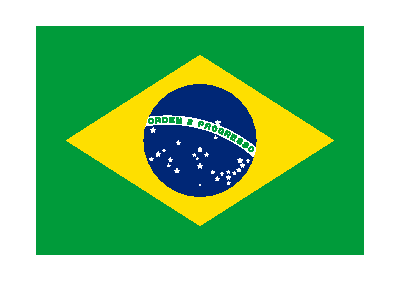

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
EntityValue[{Entity["Country","UnitedStates"],Entity["Country","Brazil"],Entity["Country","China"]},"Flag"]
```

The Wolfram Language has deep knowledge about countries, as about many other things.

Find out how many radio stations there are in the list of countries:

```mathematica
EntityValue[{Entity["Country","UnitedStates"],Entity["Country","Brazil"],Entity["Country","China"]},"RadioStations"]
```

{13769,1822,673}

Make a pie chart of the results:

```mathematica
PieChart[EntityValue[{Entity["Country","UnitedStates"],Entity["Country","Brazil"],Entity["Country","China"]},"RadioStations"]]
```

-Graphics-

Find countries that border Switzerland:

```mathematica
Entity["Country","Switzerland"]["BorderingCountries"]
```

{Austria,France,Germany,Italy,Liechtenstein}

Find their flags:

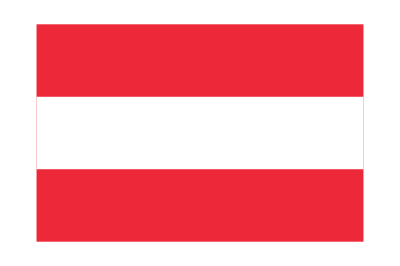


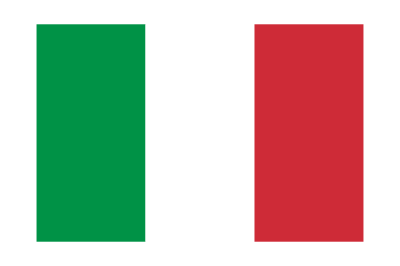
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
EntityValue[Entity["Country","Switzerland"]["BorderingCountries"],"Flag"]
```

Sometimes you’ll want to talk about a class of entities—like, say, planets.

Ask for planets, and get the class of entities corresponding to planets:

```mathematica
LinguisticAssistant
```

planets

Classes of entities are indicated by . You can get a list of all entities in a class using EntityList.

Get the list of planets:

```mathematica
EntityList[EntityClass["Planet",All]]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

Get images of all of the planets:

```mathematica
EntityValue[EntityClass["Planet",All],"Image"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

EntityValue can actually handle entity classes directly, so you don’t need to use EntityList with it.

Get the radius of each of the planets, and make a bar chart of them:

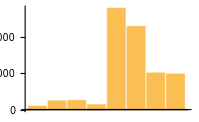

```mathematica
BarChart[EntityValue[EntityClass["Planet",All],"Radius"]]
```

It’s very convenient to use plain English to describe things. But a downside is that it can be ambiguous. If you say “mercury”, do you mean the planet Mercury or the chemical element mercury or something else called “mercury”? When you use ctrl=, it’ll always make an initial choice. But if you press the  you can change to another choice. Press the check mark  to accept a choice.

```mathematica
LinguisticAssistant
```

To see how the Wolfram Language internally represents entities you can use InputForm.

Show the internal form of the entity that represents the United States:

```mathematica
InputForm[LinguisticAssistant]
```

Entity["Country", "UnitedStates"]

Show the internal form for New York City:

```mathematica
InputForm[LinguisticAssistant]
```

Entity["City", {"NewYork", "NewYork", "UnitedStates"}]

There are millions of entities in the Wolfram Language, each with a definite internal form. In principle you could enter any entity using its internal form. But unless you’re using the same entity over and over again, it’s much more practical just to use ctrl= and enter a name for the entity in plain English.

There are thousands of different types of entities in the Wolfram Language, covering all sorts of areas of knowledge. To find out about them, check out the Wolfram Language documentation, or the Wolfram|Alpha examples pages. Each type of entity then has a list of properties—often hundreds of them. One way to find this list is to use EntityProperties.

Possible properties for amusement parks:

```mathematica
EntityProperties["AmusementPark"]
```

```mathematica
{EntityProperty["AmusementPark","AdministrativeDivision"],EntityProperty["AmusementPark","AmusementParkType"],EntityProperty["AmusementPark","Area"],EntityProperty["AmusementPark","City"],EntityProperty["AmusementPark","ClosingDate"],EntityProperty["AmusementPark","Coordinates"],EntityProperty["AmusementPark","Country"],EntityProperty["AmusementPark","EntityClasses"],EntityProperty["AmusementPark","EntityTypeList"],EntityProperty["AmusementPark","Image"],EntityProperty["AmusementPark","Latitude"],EntityProperty["AmusementPark","Longitude"],EntityProperty["AmusementPark","Name"],EntityProperty["AmusementPark","NumberOfRides"],EntityProperty["AmusementPark","OpeningDate"],EntityProperty["AmusementPark","Owner"],EntityProperty["AmusementPark","PoolCount"],EntityProperty["AmusementPark","Position"],EntityProperty["AmusementPark","RollerCoasterCount"],EntityProperty["AmusementPark","Season"],EntityProperty["AmusementPark","SlideCount"],EntityProperty["AmusementPark","Slogan"],EntityProperty["AmusementPark","StandardRides"],EntityProperty["AmusementPark","Status"],EntityProperty["AmusementPark","WaterRideCount"],EntityProperty["AmusementPark","Website"]}
```

In practice, though, a good approach is to ask in plain English for a property of some entity, then to look at the interpretation that’s found, and reuse the property from it.

Ask for the height of the Eiffel Tower:

```mathematica
LinguisticAssistant
```

```mathematica
LinguisticAssistant
```

1062.99 ft

Reuse the "Height" property, applied to the Great Pyramid:

```mathematica
Entity["Building","GreatPyramidOfGiza::jbm66"]["Height"]
```

456.037 ft

Different types of entities have different properties. One common property for many types of entities is "Image".

Get images of various entities:

```mathematica
Entity["Species","Species:PhascolarctosCinereus"]["Image"]
```

-Graphics-

```mathematica
Entity["Building","EiffelTower::5h9w8"]["Image"]
```

-Graphics-

```mathematica
Entity["Artwork","TheStarryNight::VincentVanGogh"]["Image"]
```

-Graphics-

```mathematica
Entity["Person","StephenWolfram::j276d"]["Image"]
```

-Graphics-

Other types of objects have other properties.

A plot of a caffeine molecule:

```mathematica
Entity["Chemical","Caffeine"]["MoleculePlot"]
```

-Graphics-

Rotatable 3D graphics of a skull:

```mathematica
Entity["AnatomicalStructure","Skull"]["Graphics3D"]
```

-Graphics-

A net that folds up into our 3D company logo:

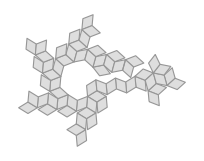

```mathematica
Entity["Polyhedron","RhombicHexecontahedron"]["NetImage"]
```

You can use RandomEntity to find random entities of a given type.

5 random musical instruments:

```mathematica
RandomEntity["MusicalInstrument", 5]
```

{paixiao,mellophone,uilleann pipes,handle lute,cimbasso}

Poster images for 5 random movies:

```mathematica
EntityValue[RandomEntity["Movie", 5],"Image"]
```

```mathematica
{-Graphics-,-Graphics-,Missing["NotAvailable"],-Graphics-,-Graphics-}
```

There’s a Missing in the list to indicate that a poster for one of the movies that was randomly picked wasn’t available in the Wolfram Knowledgebase. You can use DeleteMissing to get rid of Missing[...] elements in a list.

Vocabulary

ctrl=   |   | plain English input 
EntityList[class] |   | entities in a class 
EntityValue[entities,property] |   | value of a property of an entity 
EntityProperties[type] |   | list of properties for an entity type 
RandomEntity[type,n] |   | a list of n random entities of a given type
InputForm[entity] |   | internal Wolfram Language representation of an entity

"13 Exercises Available"
"with 3 extras" | "Get Started »"

Find the flag of Switzerland. »

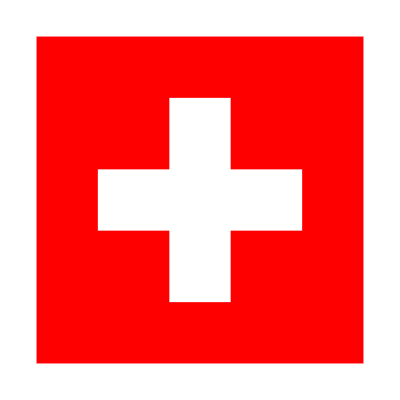
| Expected output: |  
  | -Graphics- |

Get an image of an elephant. »

| Sample expected output: |  
  | -Graphics- |

Use the "Mass" property to generate a list of the masses of the planets. »

| Expected output: |  
  | {3.30104×10^23 "kg",4.86732×10^24 "kg",5.9721986×10^24 "kg",6.41693×10^23 "kg",1.89813×10^27 "kg",5.68319×10^26 "kg",8.68103×10^25 "kg",1.0241×10^26 "kg"} |

Make a bar chart of the masses of the planets. »

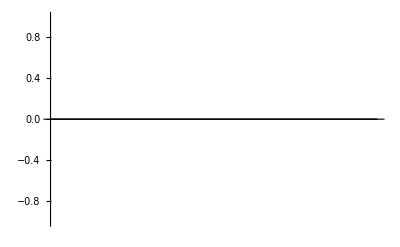
| Expected output: |  
  | -Graphics- |

Make an image collage of images of the planets. »

| Expected output: |  
  | -Graphics- |

Edge detect the flag of China. »

| Expected output: |  
  | -Graphics- |

Find the height of the Empire State Building. »

| Expected output: |  
  | 1250. "ft" |

Compute the height of the Empire State Building divided by the height of the Great Pyramid. »

| Expected output: |  
  | 2.74101 |

Compute the elevation of Mount Everest divided by the height of the Empire State Building. »

| Expected output: |  
  | 23.2231 |

Find the dominant colors in the painting The Starry Night. »

| Expected output: |  
  | {RGBColor[0.333210073303407, 0.4351874611175525, 0.6023100342028767],RGBColor[0.14034756340914756, 0.14880903369475215, 0.1328084784973558],RGBColor[0.4972573447416196, 0.5560651909750424, 0.5124431010476901],RGBColor[0.7205755102806681, 0.6443868305594601, 0.155186863494116]} |

Find the dominant colors in an image collage of the flag images of all countries in Europe. »

| Expected output: |  
  | {RGBColor[0.8183425584173621, 0.08122308489604538, 0.126435042168092],RGBColor[0.9982486174111175, 0.9976063417674855, 0.9980450366458696],RGBColor[0.09042354455069057, 0.26314276888217375, 0.6330421732829207],RGBColor[0.9946601933524518, 0.8230895429168614, 0.06267380055108188],RGBColor[0.02203692301018112, 0.12674817593653714, 0.587059140625245],RGBColor[0.26547798521261845, 0.6767626219948875, 0.8834869687704909],RGBColor[0.001592510117638875, 0.5869160722226756, 0.277251643699218],RGBColor[0.0018772829353379725, 0.0002632333216638855, 0.00022807077974769458],RGBColor[0.003223156972888176, 0.4703712362318783, 0.2912852956271836],RGBColor[0.6205944459906476, 0.18941417038613217, 0.22461341753642677],RGBColor[0.8149049335765184, 0.6518362504173659, 0.25222077496297374],RGBColor[0.005644646847697775, 0.39880402112493174, 0.00012004920652500555],RGBColor[0.9902908758583785, 0.47183671946988, 0.0027783983661768446]} |

Make a pie chart of the GDP of countries in Europe. »

| Expected output: |  
  | -Graphics- |

Add an image of a koala to an image of the Australian flag. »

| Sample expected output: |  
  | -Graphics- |

Make an image collage of the flags of all countries in Europe, using the "FlagImage" property. »

| Expected output: |  
  | -Graphics- |

Edge detect an image of the painting The Starry Night. »

| Expected output: |  
  | -Graphics- |

Color negate the Mona Lisa painting. »

| Expected output: |  
  | -Graphics- |

Q&A

Where does the Wolfram Language get its real-world data?

It’s all from the central Wolfram Knowledgebase. We’ve been building this knowledgebase for many years, carefully curating data from thousands of primary sources.

Is the data in the Wolfram Language regularly updated?

Yes. We put a lot of effort into keeping it all up to date. And in fact there’s new data flowing in every second—about market prices, weather, earthquakes, aircraft positions and lots more.

How accurate is the data in the Wolfram Language?

We go to a lot of trouble to make it as accurate as possible, and we check it extensively. But ultimately we often have to rely on what governments and other outside organizations report.

What is the relation to Wolfram|Alpha?

Wolfram|Alpha uses the same knowledgebase as the Wolfram Language.

How should I ask for a particular entity?

However you want to. The Wolfram Language is set up to understand all common ways to refer to entities. (“New York City”, “NYC”, “the big apple”, etc., all work.)

How should I cite data that I get from the Wolfram Language?

Wolfram Knowledgebase (2023) (or whatever year you retrieve it). You can also link to the documentation for the entity type you’re using, such as https://reference.wolfram.com/language/ref/entity/Country.html.

How can I find all properties and values for a given entity?

Use entity["Dataset"] or entity["PropertyAssociation"]. You can also look up documentation about any type of entity in the Wolfram Language Documentation Center.

Why might EntityValue give Missing[...]?

Most often it’s because the value needed simply isn’t available from any source that’s been curated for the Wolfram Knowledgebase. Sometimes it’s because the value doesn’t apply, like the boiling point of a chemical that decomposes but never boils.

Can I set up my own entities, and put in my own data about them?

Yes, using EntityStore.

Tech Notes

The Wolfram Knowledgebase is stored in the cloud, so even if you’re using a desktop version of the Wolfram Language, you’ll need to connect to the network to start getting real-world data.

The Wolfram Knowledgebase contains many trillions of specific facts and values, stored in a Wolfram Language symbolic framework, with a variety of underlying database technologies.

The Wolfram Knowledgebase has been systematically built and curated from large numbers of primary sources of data. It doesn’t come from web searching.

Real-world data often involves units, which we’ll discuss in the next section.

If you want to find more information about the original source of a particular piece of data, you can look at the documentation for that entity type, or you can ask for the data in Wolfram|Alpha and follow source links. You can find it programmatically using EntityValue[entity, property,"Source"].

Sometimes you want to talk about a special instance of an entity, like a country in a particular year, or a certain amount of a substance. You can do this using constructs like Dated (discussed in Section 19) or EntityInstance.

There’s a symmetry between entities and properties. entity[property] gives the same result as property[entity]. To get values of several properties, use entity[{p_1, p_2, ...}]; to get values for several entities, use property[{e_1, e_2, ...}]. (Note that for property[entity] you need the full property object, as obtained from ctrl=, not just the name of the property as a string.)

The Wolfram Language supports implicit entity classes such as “countries with more than 100 million people”. Access these using natural language, or using constructs like property→GreaterThan[10^7], etc.

More to Explore

Major Areas Covered by the Wolfram Knowledgebase »

Geographic Data and Computation »

Scientific and Medical Data and Computation »

Engineering Data and Computation »

Social, Cultural and Linguistic Data »